```mathematica
ClearAll["Global`*"];
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
tt=-f0[r,θ]* H[r]+ f2[r,θ]*r^2*Sin[θ]^2W[r,θ]^2;
rr=f1[r,θ]/H[r] ;
θθ=f1[r,θ]*r^2;
ϕϕ=f2[r,θ]* r^2*Sin[θ]^2;
tϕ=-f2[r,θ]*r^2*Sin[θ]^2W[r,θ];
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
Rtor[R_] := R - a^2/RH;
```

```mathematica
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
```

```mathematica
rh=1; ct=-0.5;
christoffel[[1,1,2]] ;
christoffel[[1,1,2]]  /. r-> 5 /. θ -> π/2;
```

```mathematica
riemann:=riemann=Table[
D[christoffel[[i,j,l]],coords[[k]]]
 - D[christoffel[[i,j,k]],coords[[l]]]
+ Sum[christoffel[[i,k,s]]christoffel[[s,j,l]] 
-christoffel[[i,l,s]]christoffel[[s,j,k]] 
,{s,1,n}]
,{i,1,n},{j,1,n},{k,1,n},{l,1,n}]
ricciT := ricciT =Table[
 Sum[riemann[[s,i,s,j]],{s,1,n}] 
,{i,1,n},{j,1,n}]
ricciS := ricciS = Sum[ricciT[[i,j]]inversemetric[[i,j]],{i,1,n},{j,1,n}]
einsteinEqn := einsteinEqn = Table[
ExpandAll[ricciT[[i,j]] - 1/2 * ricciS  metric[[i,j]]]
,{i,1,n},{j,1,n}]
einsteinEqnUp := einsteinEqnUp = Table[
Sum[einsteinEqn[[i,s]]*inversemetric[[s,j]],{s,1,n}]
,{i,1,n},{j,1,n}]
```

```mathematica
f0[r_,t_]:=  1/f2[r,t] 
H[r_]:=1-rh/r;
f1[r_,θ_]:=   (1-ct/r)^2+(ct (ct-rh) Cos[θ]^2)/r^2   ;
f2[r_,θ_]:=  1/((1-ct/r)^2+(ct (ct-rh) Cos[θ]^2)/r^2)(( (1-ct/r)^2+ (ct (ct-rh))/r^2)^2 +ct (rh-ct)(1-rh/r) Sin[θ]^2/r^2);

W[r_,θ_]:=  (1-ct/r)/r^3(√(ct (ct-rh))(rh-2 ct))/(( (1-ct/r)^2+ (ct (ct-rh))/r^2)^2 +ct (rh-ct)(1-rh/r) Sin[θ]^2/r^2);
```

```mathematica
Table[FullSimplify[einsteinEqnUp[[i,j]],x>0&&rH>0&&p>0&&θ>0&&θ<Pi],{i,1,n},{j,1,n}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. 
it calculates whether the trajectory is timelike or null from the variable χ and uinvar which is determined before 
calling the function *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(Re[r[τ]]≤1.01*rh),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler 
I want to plot in the R, i.e. BL, radial coordinates, so for solution 1, I have to translate to R via r = R - a^2/RH *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=(r[τ]+a^2/RH) Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=(r[τ]+a^2/RH) Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=(r[τ]+a^2/RH) Cos[θ[τ]]/.soln;{xs,ys,zs}]
coordlist[τin_,soln_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

```mathematica
genXYPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
```

```mathematica
τend=.;uinvar = 0;
rh=1.0;ct=-0.5;
M=(rh-2ct)/2.0
a = Sqrt[ct(ct-rh)](rh-2ct)/2
RH = M+Sqrt[M^2-a^2];
(* Since we are plotting in the BL space, the horizon is at RH, not rh *)
horizpl=PolarPlot[RH,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=100;
```

1.

0.866025

```mathematica
soln=computeSoln[τPlot,{-0.1,0,0.01},{0,Rtor[8 RH],π/2,0}];
xyzsoln=sphslnToCartsln[soln];
Table[{τi,coords[[2]][τ] /. soln /. τ -> τi},{τi,0,100,1}]
```

{{0,{11.5}},{1,{11.4005}},{2,{11.3019}},{3,{11.2042}},{4,{11.1076}},{5,{11.012}},{6,{10.9173}},{7,{10.8238}},{8,{10.7313}},{9,{10.6399}},{10,{10.5497}},{11,{10.4606}},{12,{10.3727}},{13,{10.286}},{14,{10.2005}},{15,{10.1163}},{16,{10.0333}},{17,{9.95167}},{18,{9.87138}},{19,{9.79245}},{20,{9.71491}},{21,{9.6388}},{22,{9.56414}},{23,{9.49096}},{24,{9.41929}},{25,{9.34916}},{26,{9.2806}},{27,{9.21364}},{28,{9.1483}},{29,{9.08462}},{30,{9.02263}},{31,{8.96235}},{32,{8.90382}},{33,{8.84706}},{34,{8.7921}},{35,{8.73897}},{36,{8.6877}},{37,{8.63831}},{38,{8.59083}},{39,{8.5453}},{40,{8.50172}},{41,{8.46014}},{42,{8.42056}},{43,{8.38303}},{44,{8.34755}},{45,{8.31415}},{46,{8.28286}},{47,{8.25368}},{48,{8.22664}},{49,{8.20176}},{50,{8.17905}},{51,{8.15853}},{52,{8.14021}},{53,{8.1241}},{54,{8.11021}},{55,{8.09856}},{56,{8.08914}},{57,{8.08197}},{58,{8.07706}},{59,{8.0744}},{60,{8.074}},{61,{8.07585}},{62,{8.07996}},{63,{8.08632}},{64,{8.09493}},{65,{8.10578}},{66,{8.11887}},{67,{8.13419}},{68,{8.15172}},{69,{8.17146}},{70,{8.19339}},{71,{8.21749}},{72,{8.24376}},{73,{8.27217}},{74,{8.30271}},{75,{8.33536}},{76,{8.3701}},{77,{8.4069}},{78,{8.44575}},{79,{8.48662}},{80,{8.52948}},{81,{8.57432}},{82,{8.62111}},{83,{8.66981}},{84,{8.72041}},{85,{8.77288}},{86,{8.82719}},{87,{8.88331}},{88,{8.94121}},{89,{9.00087}},{90,{9.06225}},{91,{9.12533}},{92,{9.19008}},{93,{9.25646}},{94,{9.32446}},{95,{9.39403}},{96,{9.46515}},{97,{9.53779}},{98,{9.61192}},{99,{9.68752}},{100,{9.76455}}}

{{0,{11.5}},{1,{11.4005}},{2,{11.3019}},{3,{11.2042}},{4,{11.1076}},{5,{11.012}},{6,{10.9173}},{7,{10.8238}},{8,{10.7313}},{9,{10.6399}},{10,{10.5497}},{11,{10.4606}},{12,{10.3727}},{13,{10.286}},{14,{10.2005}},{15,{10.1163}},{16,{10.0333}},{17,{9.95167}},{18,{9.87138}},{19,{9.79245}},{20,{9.71491}},{21,{9.6388}},{22,{9.56414}},{23,{9.49096}},{24,{9.41929}},{25,{9.34916}},{26,{9.2806}},{27,{9.21364}},{28,{9.1483}},{29,{9.08462}},{30,{9.02263}},{31,{8.96235}},{32,{8.90382}},{33,{8.84706}},{34,{8.7921}},{35,{8.73897}},{36,{8.6877}},{37,{8.63831}},{38,{8.59083}},{39,{8.5453}},{40,{8.50172}},{41,{8.46014}},{42,{8.42056}},{43,{8.38303}},{44,{8.34755}},{45,{8.31415}},{46,{8.28286}},{47,{8.25368}},{48,{8.22664}},{49,{8.20176}},{50,{8.17905}},{51,{8.15853}},{52,{8.14021}},{53,{8.1241}},{54,{8.11021}},{55,{8.09856}},{56,{8.08914}},{57,{8.08197}},{58,{8.07706}},{59,{8.0744}},{60,{8.074}},{61,{8.07585}},{62,{8.07996}},{63,{8.08632}},{64,{8.09493}},{65,{8.10578}},{66,{8.11887}},{67,{8.13419}},{68,{8.15172}},{69,{8.17146}},{70,{8.19339}},{71,{8.21749}},{72,{8.24376}},{73,{8.27217}},{74,{8.30271}},{75,{8.33536}},{76,{8.3701}},{77,{8.4069}},{78,{8.44575}},{79,{8.48662}},{80,{8.52948}},{81,{8.57432}},{82,{8.62111}},{83,{8.66981}},{84,{8.72041}},{85,{8.77288}},{86,{8.82719}},{87,{8.88331}},{88,{8.94121}},{89,{9.00087}},{90,{9.06225}},{91,{9.12533}},{92,{9.19008}},{93,{9.25646}},{94,{9.32446}},{95,{9.39403}},{96,{9.46515}},{97,{9.53779}},{98,{9.61192}},{99,{9.68752}},{100,{9.76455}}}

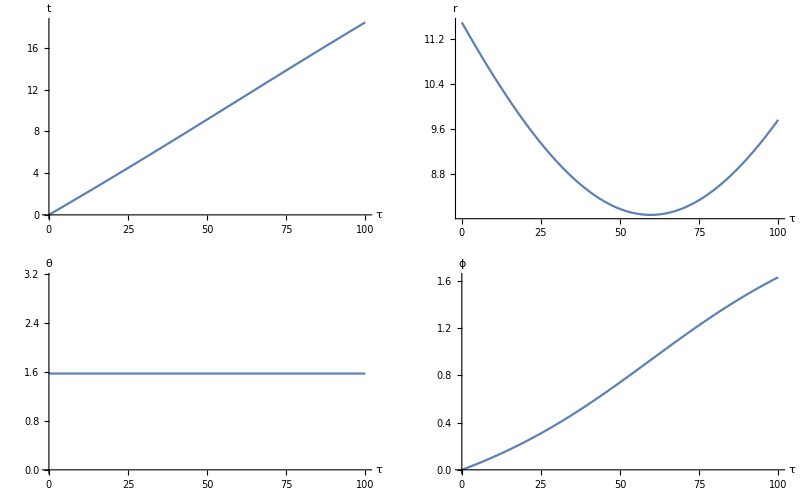

```mathematica
GraphicsGrid[{{Plot[{Evaluate[coords[[1]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","t"}],Plot[{Evaluate[coords[[2]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","r"}]},{Plot[{Evaluate[coords[[3]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","θ"}],Plot[{Evaluate[coords[[4]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","ϕ"}]}}]
```

For initial coordinates={0,5.5,π/2,0} and initial velocities={-0.1,0,0.01} the particle crosses the horizon at τend=75.0199

With final coordinates={t = 35.1254,r = 1.01,θ = 1.5708,ϕ = 9.38105}

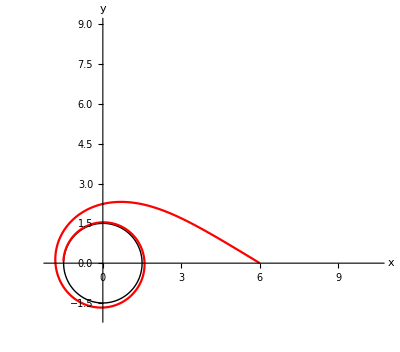

```mathematica
(* first one, in red, is other Kerr and the second one, in blue, is BL Kerr *)
genXYPlot[τPlot,{0,Rtor[4 RH],π/2,0},{-0.1,0,0.01},1];
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-2,7RH},{-2,6RH}}]
```

```mathematica
(* other coords *)
a
M
rh
ct
tt/.r->Rtor[10]/.θ->π/2
rr/.r->Rtor[10]/.θ->π/2
θθ/.r->Rtor[10]/.θ->π/2
ϕϕ/.r->Rtor[10]/.θ->π/2
christoffel[[1,1,2]]  /. r-> Rtor[10] /. θ -> π/2
christoffel[[2,2,2]]  /. r-> Rtor[10] /. θ -> π/2
christoffel[[2,1,1]]  /. r-> Rtor[10] /. θ -> π/2
christoffel[[3,3,2]]  /. r-> Rtor[10] /. θ -> π/2
```

0.866025

1.

1

-0.5

-0.8

1.23839

100.

100.9

0.0124768

-0.0114551

0.008075

0.1